# Tipos de Entrada Titulo “Alt+1”

## Capitulo “Alt+2”

Subcapitulo “Alt+3”

## Seccion “Alt+4”

### Subseccion “Alt+5”

#### Subsubseccion “Alt+6”

Texto “Alt+7”

```mathematica
Codigo(*Texto y codigo estan el la misma jerarquia*) "Alt+8"
```

Alt+8 Codigo

sdfaaaaaaaaaaaaaaaa

Brayhan

Alejandro

aaaaaaaaaaa

aaaaaaaaa

aaaaaaa

alex

asdd

aaaaaa

∫x yⅆx d 			Formula de Euler

Integrate[Sin[x^2],x]                    (* Formula de Display*)

Integrate[a s,s]                                  (*Formula de Display numerada ---> *)

Programa

```mathematica
x=2 b+c*b
```

2 b+b c

# Plot in Mathematica

### Plot in Mathematica

```mathematica
??Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
?PlotPoints
```

PlotPoints is an option for plotting functions that specifies how many initial sample points to use.

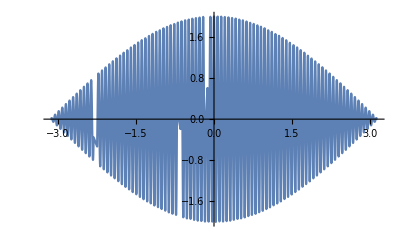

```mathematica
Plot[Cos[90t]+Cos[91t],{t,-Pi,Pi}]
```

Esta grafica es incorrecta ya que Mathematica no cuenta con los puntos suficientes para graficar de manera adecuada

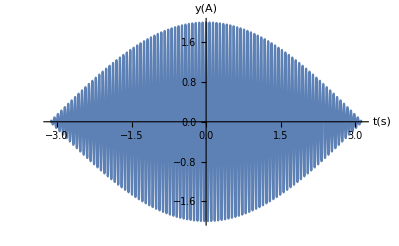

```mathematica
Plot[Cos[90t]+Cos[91t],{t,-Pi,Pi},PlotPoints->200,AxesLabel->{"t(s)","y(A)"}]
```

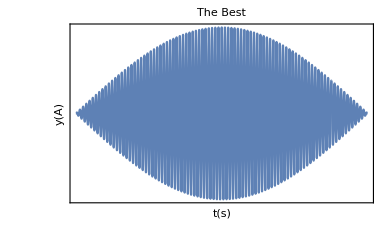

```mathematica
Plot[Cos[90t]+Cos[91t],{t,-Pi,Pi},PlotPoints->200,Axes->False,PlotLabel->"The Best", Frame->True(*Marco*),FrameTicks->None(*Graduacion de marco*),FrameLabel->{"t(s)","y(A)"}]
```

```mathematica
f[x_]:=x^2 -2x;
g[x_]:=Sin[x];
```

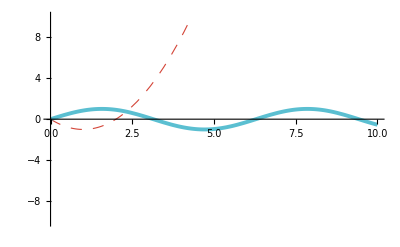

```mathematica
Plot[{f[x],g[x]},{x,0,10},PlotRange->{-10,10},PlotStyle->{{Thickness[0.002](*Grosor de la linea*),Dashing[0.02](*Punteo*),RGBColor[0.83,0.27,0.22]},{Thickness[0.007],GrayLevel[0.63,0.84],RGBColor[0.23,0.7,0.79]}}]
```

```mathematica
FindRoot[Sin[x]==x^2,{x,xycoord[[1]]}]
```

Part::partd: Part specification xycoord ⟦ 1 ⟧ is longer than depth of object.

FindRoot::srect: Value xycoord ⟦ 1 ⟧ in search specification {x, xycoord ⟦ 1 ⟧} is not a number or array of numbers.

FindRoot[Sin[x]==x^2,{x,xycoord⟦1⟧}]

```mathematica
FindRoot[Sin[x]==x^2,{x,0.8}]
```

{x→0.876726}

```mathematica
??#
```

# represents the first argument supplied to a pure function. 
#n represents the n^th argument. 
#name represents the value associated with key "name" in an association in the first argument.

Attributes[Slot]={NHoldAll,Protected}

```mathematica
Clear[x]
```

```mathematica
NSolve[Sin[x]==x^2,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Sin[x]==x^2,x]

```mathematica
??ClickPane
```

ClickPane[image,func] represents a clickable pane that displays as image and applies func to the x,y coordinates of each click within the pane.
ClickPane[image,{{x_min,y_min},{x_max,y_max}},func] specifies the range of coordinates to use.

Attributes[ClickPane]={Protected,ReadProtected}
 
Options[ClickPane]={Method→Preemptive,PassEventsDown→Automatic,PassEventsUp→True}

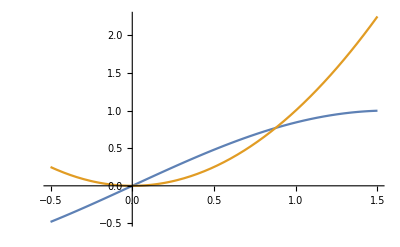

```mathematica
ClickPane[Plot[{Sin[x],x^2},{x,-.5,1.5}],(xycoord=#)&]
```

```mathematica
FindRoot[Sin[x]==x^2,{x,xycoord[[1]]}]
```

{x→-2.97141×10^-15}

#### Data Plot

```mathematica
misDatos={{1,1.1},{2,2.2},{3,3},{4.1,4},{5.5,5},{6,6},{7,7}};
```

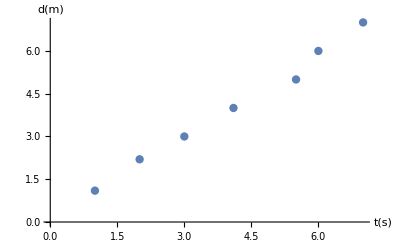

```mathematica
ListPlot[misDatos,PlotStyle->PointSize[0.015],AxesLabel->{"t(s)","d(m)"}]
```

Diferencias entre Plot y Parametric Pot

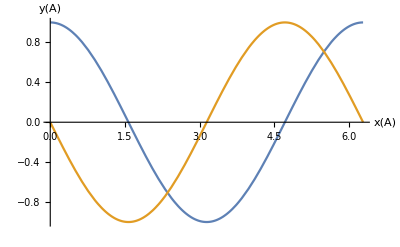

```mathematica
Plot[{Cos[t],Cos[t+(Pi/2)]},{t,0,2*Pi},AxesLabel->{"x(A)","y(A)"}]
```

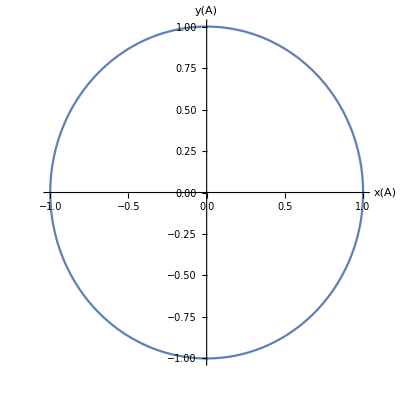

```mathematica
ParametricPlot[{Cos[t],Cos[t+(Pi/2)]},{t,0,2*Pi},AxesLabel->{"x(A)","y(A)"}]
```

```mathematica
??ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions. 
ParametricPlot[…,{u,v}∈reg] takes parameters {u,v} to be in the geometric region reg.

Attributes[ParametricPlot]={HoldAll,Protected,ReadProtected}
 
Options[ParametricPlot]={AlignmentPoint→Center,AspectRatio→Automatic,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→Automatic,MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

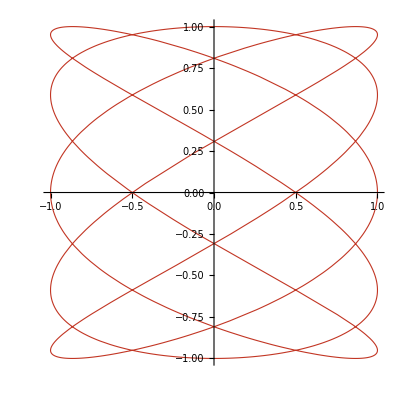

```mathematica
ParametricPlot[{Cos[5t],Sin[3t]},{t,0,2Pi},PlotStyle->{RGBColor[0.76,0.21,0.14], Thickness[0.002]}]
```

```mathematica
Manipulate[Plot[Evaluate[x[t]/.NDSolve[{x''[t]+2β x'[t]+4x[t]==0,x[0]==1,x'[0]==0},x,{t,0,50}]],{t,0,50},AxesLabel->{"t(s)","x(m)"},PlotRange->{-1,1}],{{β,0,"Coeficiente β(s⁻.b9)"},0,1.9,0.1}]
```

```mathematica
Animate[Plot[{E^(-16 (x-t)^2)+1.5E^(-(x+t)^2),1.5E^(-(x+t)^2)+ 3,E^(-16 (x-t)^2)+5},{x,-3,3},PlotStyle->{{Thickness[0.001],Black},{Thickness[0.005],Red},{Thickness[0.005],Blue}},PlotRange->{-.1,7}],{t,-2,3.5}]
```

#### Definicion de Onda estacionaria

```mathematica
Animate[Plot[{2Sin[x+2t]+8,2Sin[-x+2t],4Cos[x]*Sin[2t]-10},{x,-10,10},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Blue},{Thickness[0.01],Black}},PlotRange->{-15,15}],{t,-2,3.5}]
```

```mathematica
Animate[ParametricPlot3D[{r*Cos[θ],r*Sin[θ],BesselJ[2,r] Sin[2θ] Cos[(Pi/8) i] },{r,0,5.13562},{θ,0,2Pi},PlotRange->{{-5,5},{-5,5},{-.5,.5}},PlotPoints->50,BoxRatios->{1,1,.4},ViewPoint->{2.34, -2.4, 2},Boxed->False,Axes->False],{i,0,15,1}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
r1[x_,y_]:=Sqrt[(x-10)^2 +y^2];
r2[x_,y_]:=Sqrt[(x+10)^2 +y^2];
z1[r1_,t_]:=Sin[r1-t]/r1;
z2[r2_,t_]:=Sin[r2-t]/r2;
z[x_,y_,t_]:=z1[r1[x,y],t ]+z2[r2[x,y],t ];
```

```mathematica
ListAnimate[Table[Plot3D[Evaluate[z[x,y,t]],{x,-25,25},{y,1,75},PlotPoints->50,PlotRange->{0,1.5} ,ViewPoint->{1.181, 3.09, 0.713},Boxed->False,Axes->False,Mesh->None],{t,0,Pi,Pi/8}]]
```

# Listas y Arreglos

```mathematica
??Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

Attributes[Range]={Listable,Protected}

```mathematica
miLista=Range[20,50,3]
```

{20,23,26,29,32,35,38,41,44,47,50}

```mathematica
??Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

Attributes[Table]={HoldAll,Protected}

```mathematica
Table[1+Sin[x]^n,{n,1,7,2}]
```

{1+Sin[x],1+Sin[x]^3,1+Sin[x]^5,1+Sin[x]^7}

```mathematica
otraLista=Table[x^i+y^j,{i,3},{j,4}]
```

{{x+y,x+y^2,x+y^3,x+y^4},{x^2+y,x^2+y^2,x^2+y^3,x^2+y^4},{x^3+y,x^3+y^2,x^3+y^3,x^3+y^4}}

```mathematica
TableForm[otraLista]
```

x+y | x+y^2 | x+y^3 | x+y^4
x^2+y | x^2+y^2 | x^2+y^3 | x^2+y^4
x^3+y | x^3+y^2 | x^3+y^3 | x^3+y^4

Herramientas para las listas y arreglos

```mathematica
Length[miLista]
```

11

```mathematica
Dimensions[otraLista]
```

{3,4}

```mathematica
cargas={{1,0,0,1},{-1,0,0,-1}}
```

{{1,0,0,1},{-1,0,0,-1}}

#### Example

```mathematica
Needs["BarCharts`"]
```

General::obspkg: "BarCharts`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
result=RandomInteger[{1,6},10^2]
```

{3,6,4,5,4,1,1,5,1,4,4,1,2,4,4,4,2,6,3,5,5,1,2,1,4,3,2,2,6,1,6,6,3,2,4,4,5,5,4,2,1,1,5,6,2,1,6,6,4,6,2,3,2,4,4,4,4,1,6,6,2,5,5,4,6,6,2,3,6,5,2,4,6,5,5,4,4,1,1,3,1,3,2,4,1,4,6,2,6,5,1,5,6,1,5,6,4,5,1,3}

```mathematica
??ScientificForm
```

ScientificForm[expr] prints with all real numbers in expr given in scientific notation. 
ScientificForm[expr,n] prints with numbers given to n-digit precision.

Attributes[ScientificForm]={Protected}
 
Options[ScientificForm]={DigitBlock→∞,ExponentFunction→Automatic,ExponentStep→1,NumberFormat→Automatic,NumberMultiplier→×,NumberPadding→{,},NumberPoint→.,NumberSeparator→{,, },NumberSigns→{-,},SignPadding→False}

```mathematica
Length[result]//ScientificForm
```

100

```mathematica
Counts[result]
```

<|3→9,6→19,4→23,5→16,1→18,2→15|>

```mathematica
Count[result,2]
```

15

```mathematica
dist=Table[Count[result,i],{i,1,6}](*Misma funcionalidad que Counts[]*)
```

{18,15,9,23,16,19}

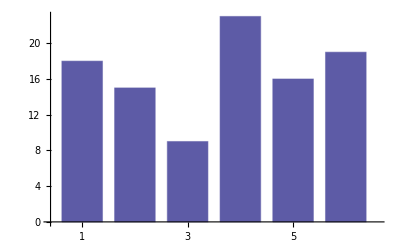

```mathematica
BarChart[dist]
```

#### Obtener Elementos de Listas y SubListas

```mathematica
??List
```

{e_1,e_2,…} is a list of elements.

Attributes[List]={Locked,Protected}

```mathematica
a={{123,1,2,3},{2,3,44,3},{2,3,2,222},{2,4,3,2}};
s=MatrixForm[a];
First[a]
Last[a]
Part[a,3](*Se obtiene el tercer elemento*)
a[[3]](*Se observa que es equivalente al anterior*)
a[[-3]](*conteo regresivo*)
Take[a,3](*Arroja los 3 primeros*)
Take[a,-2](*Arroja los 2 ultimos*)
Take[a,{2,4}](*Arroja desde 2 hasta 4*)
s
Rest[a](*Muestra la lista sin el primer elemento*)
Most[a](*Muestra la lista sin el ultimo elemento*)
Drop[a,2](*Muestra los 2 ultimos elementos de la lista*)
Drop[a,{2,3}](*Quila los elementos del 2 al 3*)
Extract[a,{1,3}]
```

{123,1,2,3}

{2,4,3,2}

{2,3,2,222}

{2,3,2,222}

{2,3,44,3}

{{123,1,2,3},{2,3,44,3},{2,3,2,222}}

{{2,3,2,222},{2,4,3,2}}

{{2,3,44,3},{2,3,2,222},{2,4,3,2}}

(123 | 1 | 2 | 3
2 | 3 | 44 | 3
2 | 3 | 2 | 222
2 | 4 | 3 | 2)

{{2,3,44,3},{2,3,2,222},{2,4,3,2}}

{{123,1,2,3},{2,3,44,3},{2,3,2,222}}

{{2,3,2,222},{2,4,3,2}}

{{123,1,2,3},{2,4,3,2}}

2

```mathematica
ListaA={{12,3,2},{12,3,4},{13,4,5},{2,3,1}};
ListaC={{qw,ew,rt,as,as},{gh,fg,df,sd,cd},{qw,ew,rt,as,as}};
MatrixForm[ListaA]
MatrixForm[ListaC]
```

(12 | 3 | 2
12 | 3 | 4
13 | 4 | 5
2 | 3 | 1)

(qw | ew | rt | as | as
gh | fg | df | sd | cd
qw | ew | rt | as | as)

### Formas de la matrices

```mathematica
Transpose[{{qw,ew,rt,as,as},{gh,fg,df,sd,cd},{qw,ew,rt,as,as}}]//MatrixForm
```

(qw | gh | qw
ew | fg | ew
rt | df | rt
as | sd | as
as | cd | as)

```mathematica
TableForm[{{qw,gh,qw},{ew,fg,ew},{rt,df,rt},{as,sd,as},{as,cd,as}}]
```

qw | gh | qw
ew | fg | ew
rt | df | rt
as | sd | as
as | cd | as

```mathematica
Grid[{{qw,gh,qw},{ew,fg,ew},{rt,df,rt},{as,sd,as},{as,cd,as}}]
```

qw | gh | qw
ew | fg | ew
rt | df | rt
as | sd | as
as | cd | as

### Operaciones con Matrices

```mathematica
Union[ListaA,ListaC]//TableForm
```

2 | 3 | 1 |  | 
12 | 3 | 2 |  | 
12 | 3 | 4 |  | 
13 | 4 | 5 |  | 
gh | fg | df | sd | cd
qw | ew | rt | as | as

```mathematica
Intersection[ListaA,ListaC](*421*)
```

{}